```mathematica
NS["dimer_study"]
```

```mathematica
wd="C:\\Users\\pglpm\\repositories\\neurobayes\\";
```

```mathematica
assu=(0<m1<1&&0<m2<1&&m1+m2-1<c&&0<c&&c<m1&&c<m2)
```

0<m1<1&&0<m2<1&&-1+m1+m2<c&&0<c&&c<m1&&c<m2

```mathematica
upa[s1_,s2_,a1_,a2_,l_]=Exp[a1*s1+a2*s2+l*s1*s2]
```

ⅇ^(a1 s1+a2 s2+l s1 s2)

```mathematica
za[a1_,a2_,l_]=Sum[upa[s1,s2,a1,a2,l],{s1,0,1},{s2,0,1}]
```

1+ⅇ^a1+ⅇ^a2+ⅇ^(a1+a2+l)

```mathematica
pa[s1_,s2_,a1_,a2_,l_]=FS[upa[s1,s2,a1,a2,l]/za[a1,a2,l]]
```

ⅇ^(a1 s1+a2 s2+l s1 s2)/(1+ⅇ^a1+ⅇ^a2+ⅇ^(a1+a2+l))

```mathematica
tpa[a1_,a2_,l_]=Flatten@Table[pa[s1,s2,a1,a2,l],{s1,0,1},{s2,0,1}]
```

{1/(1+ⅇ^a1+ⅇ^a2+ⅇ^(a1+a2+l)),ⅇ^a2/(1+ⅇ^a1+ⅇ^a2+ⅇ^(a1+a2+l)),ⅇ^a1/(1+ⅇ^a1+ⅇ^a2+ⅇ^(a1+a2+l)),ⅇ^(a1+a2+l)/(1+ⅇ^a1+ⅇ^a2+ⅇ^(a1+a2+l))}

```mathematica
e1pa[a1_,a2_,l_]=FS@Sum[s1*pa[s1,s2,a1,a2,l],{s1,0,1},{s2,0,1}]
```

1/(1+(1+ⅇ^a2)/(ⅇ^a1+ⅇ^(a1+a2+l)))

```mathematica
e2pa[a1_,a2_,l_]=FS@Sum[s2*pa[s1,s2,a1,a2,l],{s1,0,1},{s2,0,1}]
```

1/(1+(1+ⅇ^a1)/(ⅇ^a2+ⅇ^(a1+a2+l)))

```mathematica
cpa[a1_,a2_,l_]=FS@Sum[s1*s2*pa[s1,s2,a1,a2,l],{s1,0,1},{s2,0,1}]
```

ⅇ^(a1+a2+l)/(1+ⅇ^a1+ⅇ^a2+ⅇ^(a1+a2+l))

```mathematica
ichange={m1->e1pa[a1,a2,l],m2->e2pa[a1,a2,l],c->cpa[a1,a2,l]}
```

{m1→1/(1+(1+ⅇ^a2)/(ⅇ^a1+ⅇ^(a1+a2+l))),m2→1/(1+(1+ⅇ^a1)/(ⅇ^a2+ⅇ^(a1+a2+l))),c→ⅇ^(a1+a2+l)/(1+ⅇ^a1+ⅇ^a2+ⅇ^(a1+a2+l))}

```mathematica
change=Flatten@Assuming[assu,FS@Solve[{e1pa[a1,a2,l]==m1,e2pa[a1,a2,l]==m2,cpa[a1,a2,l]==c},{a1,a2,l},Reals]]
```

{a1→Log[(c-m1)/(-1-c+m1+m2)],a2→Log[(c-m2)/(-1-c+m1+m2)],l→Log[(c (1+c-m1-m2))/((c-m1) (c-m2))]}

```mathematica
pm[s1_,s2_,m1_,m2_,c_]=FS[pa[s1,s2,a1,a2,l]/.change]
```

(1+c-m1-m2) ((c (1+c-m1-m2))/((c-m1) (c-m2)))^(s1 s2) ((c-m1)/(-1-c+m1+m2))^s1 ((c-m2)/(-1-c+m1+m2))^s2

```mathematica
jac[m1_,m2_,c_]=Assuming[assu,FS@Det[
D[{a1,a2,l}/.change,{{m1,m2,c}}]]]
```

1/(c (c-m1) (c-m2) (1+c-m1-m2))

```mathematica
ijac[a1_,a2_,l_]=Assuming[assu,FS@Det[
D[{m1,m2,c}/.ichange,{{a1,a2,l}}]]]
```

ⅇ^(2 (a1+a2)+l)/((1+ⅇ^a1+ⅇ^a2+ⅇ^(a1+a2+l))^4)

```mathematica
FS@Det[D[Log[za[a1,a2,l]],{{a1,a2,l},2}]]
```

ⅇ^(2 (a1+a2)+l)/((1+ⅇ^a1+ⅇ^a2+ⅇ^(a1+a2+l))^4)

```mathematica
Plot3D[{Max[0,x+y-1],Min[x,y,1]},{x,0,1},{y,0,1},PlotRange->{0,1},BoxRatios->1,AxesLabel->myaxes[{Subscript[m,1],Subscript[m,2],l}],ViewPoint->Dynamic[viewpoint],PlotStyle->Opacity[0.5],Mesh->None]
```

-Graphics3D-

```mathematica
expng[wd<>"domain"]
```

C:\Users\pglpm\repositories\neurobayes\domain.png

```mathematica
inte=Integrate[jac[m1,m2,c],{c,Max[0,m1+m2-1],Min[m1,m2,1]}]
```

ConditionalExpression[Log[Max[0,-1+m1+m2]]/(m1 m2 (-1+m1+m2))+Log[-m1+Max[0,-1+m1+m2]]/(m1 (m1-m2) (-1+m2))-(Log[-m2+Max[0,-1+m1+m2]]/((m1-m2) m2)+Log[1-m1-m2+Max[0,-1+m1+m2]]/((-1+m2) (-1+m1+m2)))/(-1+m1)+(-∞)/(Sign[m1] Sign[-1+m2]),m1≤Max[0,-1+m1+m2]&&m1≤Min[1,m1,m2]]

```mathematica
Assuming[assu,FS@inte]
```

Undefined

```mathematica
ClearAll[testf];testf[x_,y_,r_:0.99]:={jac[x,y,r*Max[0,x+y-1]+(1-r)*Min[x,y,1]],jac[x,y,(1-r)*Max[0,x+y-1]+r*Min[x,y,1]]}
```

```mathematica
testf[0.01,0.01,0.99]
```

{1.04102×10^8,1.02041×10^10}

```mathematica
testf[0.99,0.99,0.99]
```

{1.04102×10^8,1.02041×10^10}

```mathematica
Integrate[6*ijac[a1,a2,l],{a1,-Infinity,Infinity},{a2,-Infinity,Infinity},{l,-Infinity,Infinity}]
```

1

```mathematica
Integrate[6*ijac[a1,a2,l],{a2,-Infinity,Infinity}]
```

ConditionalExpression[1/16 Sech[a1/2]^2 Sech[(a1+l)/2]^2,(Re[(1+ⅇ^a1)/(1+ⅇ^(a1+l))]≥0||Re[(1+ⅇ^a1)/(1+ⅇ^(a1+l))]≤-1||(1+ⅇ^a1)/(1+ⅇ^(a1+l))∉ℝ)&&(Re[(1+ⅇ^(a1+l))/(1+ⅇ^a1)]≥0||Re[(1+ⅇ^(a1+l))/(1+ⅇ^a1)]≤-1||(1+ⅇ^(a1+l))/(1+ⅇ^a1)∉ℝ)]

```mathematica
funa1l=Assuming[a1>0&&l>0,FS[%51]]
```

1/16 Sech[a1/2]^2 Sech[(a1+l)/2]^2

```mathematica
Plot3D[funa1l,{a1,-5,5},{l,-5,5},BoxRatios->{1,1,1/2},Mesh->None, AxesLabel->myaxes[{Subscript[μ,1],λ,p}],PlotPoints->50,ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
expng[wd<>"marginal_flatstat"]
```

C:\Users\pglpm\repositories\neurobayes\marginal_flatstat.png

```mathematica
zz=Integrate[6*(1+c-m1-m2)*Boole[Max[0,m1+m2-1]≤c≤Min[m1,m2]],{c,0,1},{m1,0,1},{m2,0,1}]
```

1/4

```mathematica
intem2=FS@Integrate[6*(1+c-m1-m2)/zz*Boole[Max[0,m1+m2-1]≤c≤Min[m1,m2,1]],{m2,0,1}]
```

Piecewise[{{12, c==0&&m1==0}, {12 (-1+m1)^2, (c==0&&0<m1<1)||(0<c<1&&(c==m1||(c<m1&&m1<1)))}, {0, True}}]

```mathematica
show2=Plot3D[intem2,{m1,0,1},{c,0,1},BoxRatios->{1,1,1},PlotRange->All,Mesh->None, AxesLabel->myaxes[{Subscript[m,1],l,p}],PlotPoints->50,ViewPoint->Dynamic[viewpoint],RegionFunction->Function[{x,y},y≤x]]
```

-Graphics3D-

```mathematica
expng[wd<>"marginal_m1_l"]
```

C:\Users\pglpm\repositories\neurobayes\marginal_m1_l.png

```mathematica
intem2m1=FS@Integrate[intem2,{m1,0,1}]
```

Piecewise[{{-4 (-1+c)^3, 0≤c<1}, {0, True}}]

```mathematica
parc=ParametricPlot3D[{1,c,intem2m1},{c,0,1},PlotStyle->{Thickness[0.02],red},PlotRange->All]
```

-Graphics3D-

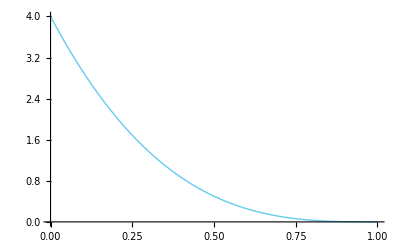

```mathematica
Plot[intem2m1,{c,0,1}]
```

```mathematica
FS@Integrate[intem2m1,{c,0,1}]
```

1

```mathematica
intem2c=FS@Integrate[intem2,{c,0,1}]
```

Piecewise[{{12 (-1+m1)^2 m1, 0<m1<1}, {0, True}}]

```mathematica
par1=ParametricPlot3D[{m1,0,intem2c},{m1,0,1},PlotStyle->{Thickness[0.02],red},PlotRange->All]
```

-Graphics3D-

```mathematica
Show[{show2,parc,par1}]
```

-Graphics3D-

```mathematica
expng[wd<>"marginal00_m1_l"]
```

C:\Users\pglpm\repositories\neurobayes\marginal00_m1_l.png

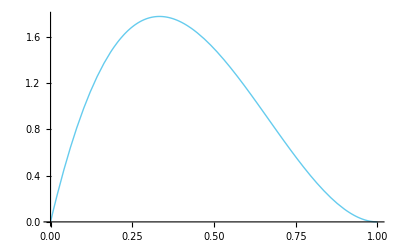

```mathematica
Plot[intem2c,{m1,0,1}]
```

```mathematica
Integrate[intem2c,{m1,0,1}]
```

1

```mathematica
zz=Integrate[6*(1+c-m1-m2)^10*Boole[Max[0,m1+m2-1]≤c≤Min[m1,m2]],{c,0,1},{m1,0,1},{m2,0,1}]
```

1/286

```mathematica
intem2=FS@Integrate[6*(1+c-m1-m2)^10/zz*Boole[Max[0,m1+m2-1]≤c≤Min[m1,m2,1]],{m2,0,1}]
```

Piecewise[{{156, c==0&&m1==0}, {-156 (-1+m1)^11, (c==0&&0<m1<1)||(0<c<1&&(c==m1||(m1<1&&c≤m1)))}, {0, True}}]

```mathematica
Plot3D[intem2,{m1,0,1},{c,0,1},BoxRatios->{1,1,1},PlotRange->All,Mesh->None, AxesLabel->myaxes[{Subscript[m,1],l,p}],PlotPoints->50,ViewPoint->Dynamic[viewpoint],RegionFunction->Function[{x,y},y≤x]]
```

-Graphics3D-

```mathematica
expng[wd<>"marginal_m1_l"]
```

C:\Users\pglpm\repositories\neurobayes\marginal_m1_l.png

```mathematica
intem2m1=FS@Integrate[intem2,{m1,0,1}]
```

Piecewise[{{13 (-1+c)^12, 0≤c<1}, {0, True}}]

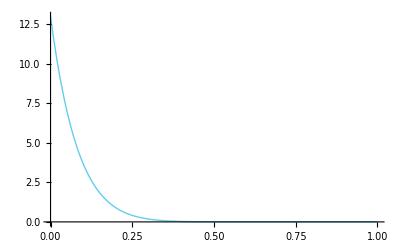

```mathematica
Plot[intem2m1,{c,0,1},PlotRange->All]
```

```mathematica
FS@Integrate[intem2m1,{c,0,1}]
```

1

```mathematica
intem2c=FS@Integrate[intem2,{c,0,1}]
```

Piecewise[{{-156 (-1+m1)^11 m1, 0<m1<1}, {0, True}}]

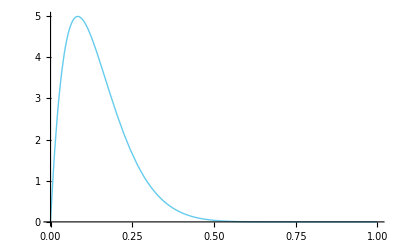

```mathematica
Plot[intem2c,{m1,0,1}]
```

```mathematica
Integrate[intem2c,{m1,0,1}]
```

1

```mathematica
zz=Integrate[6*(1+c-m1-m2)^0*Boole[Max[0,m1+m2-1]≤c≤Min[m1,m2]],{c,0,1},{m1,0,1},{m2,0,1}]
```

1

```mathematica
intem2=FS@Integrate[6*(1+c-m1-m2)^0/zz*Boole[Max[0,m1+m2-1]≤c≤Min[m1,m2,1]],{m2,0,1}]
```

Piecewise[{{6, c==0&&m1==0}, {6-6 m1, (c==0&&0<m1<1)||(0<c<1&&(c==m1||(m1<1&&c≤m1)))}, {0, True}}]

```mathematica
Plot3D[intem2,{m1,0,1},{c,0,1},BoxRatios->{1,1,1/2},PlotRange->All,Mesh->None, AxesLabel->myaxes[{Subscript[m,1],l,p}],PlotPoints->50,ViewPoint->Dynamic[viewpoint],RegionFunction->Function[{x,y},y≤x]]
```

-Graphics3D-

```mathematica
expng[wd<>"marginal_m1_l"]
```

C:\Users\pglpm\repositories\neurobayes\marginal_m1_l.png

```mathematica
intem2m1=FS@Integrate[intem2,{m1,0,1}]
```

Piecewise[{{3 (-1+c)^2, 0≤c<1}, {0, True}}]

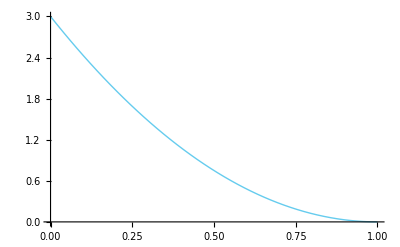

```mathematica
Plot[intem2m1,{c,0,1}]
```

```mathematica
FS@Integrate[intem2m1,{c,0,1}]
```

1

```mathematica
intem2c=FS@Integrate[intem2,{c,0,1}]
```

Piecewise[{{-6 (-1+m1) m1, 0<m1<1}, {0, True}}]

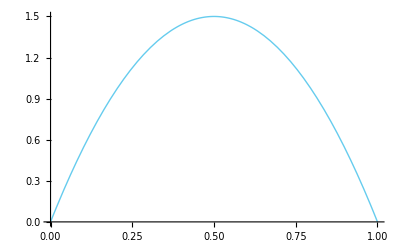

```mathematica
Plot[intem2c,{m1,0,1}]
```

```mathematica
Integrate[intem2c,{m1,0,1}]
```

1